## 1

```mathematica
Clear["Global`*"];
dim=7/2;

SpinMatrices[s_]:=Module[{d,IzMat,superDiag,Iplus,Iminus,IxMat,IyMat},(*Define the dimension of the matrices:d=2s+1*)d=2 s+1;
(*Construct Iz:a diagonal matrix with entries m=s,s-1,...,-s*)IzMat=DiagonalMatrix[Table[m,{m,s,-s,-1}]];
(*Compute the superdiagonal elements for I+*)superDiag=Table[Sqrt[s (s+1)-(s-j) (s-j+1)],{j,1,d-1}];
(*Construct I+as a dense matrix with superdiagonal elements*)Iplus=Normal[SparseArray[Band[{1,2}]->superDiag,{d,d}]];
(*Construct I-as the transpose of I+*)Iminus=Transpose[Iplus];
(*Compute Ix and Iy from I+and I-*)IxMat=(Iplus+Iminus)/2;
IyMat=(Iplus-Iminus)/(2 I);
(*Return the three spin matrices*){IxMat,IyMat,IzMat}];

(*Assign the matrices*)
{Ix3half2,Iy3half2,Iz3half2}=SpinMatrices[dim];
Hmuti[ϕ1_,ϕ2_,ϕ3_,ϕ4_,ϕ5_,ϕ6_,ϕ7_]:=({{0, (√7)/2 ⅇ^(-ⅈ ϕ1), 0, 0, 0, 0, 0, 0}, {(√7)/2 ⅇ^(ⅈ ϕ1), 0, √3 ⅇ^(-ⅈ ϕ2), 0, 0, 0, 0, 0}, {0, √3 ⅇ^(ⅈ ϕ2), 0, (√15)/2 ⅇ^(-ⅈ ϕ3), 0, 0, 0, 0}, {0, 0, (√15)/2 ⅇ^(ⅈ ϕ3), 0, 2 ⅇ^(-ⅈ ϕ4), 0, 0, 0}, {0, 0, 0, 2 ⅇ^(ⅈ ϕ4), 0, (√15)/2 ⅇ^(-ⅈ ϕ5), 0, 0}, {0, 0, 0, 0, (√15)/2 ⅇ^(ⅈ ϕ5), 0, √3 ⅇ^(-ⅈ ϕ6), 0}, {0, 0, 0, 0, 0, √3 ⅇ^(ⅈ ϕ6), 0, (√7)/2 ⅇ^(-ⅈ ϕ7)}, {0, 0, 0, 0, 0, 0, (√7)/2 ⅇ^(ⅈ ϕ7), 0}});
Iplus5half2=Ix3half2+I*Iy3half2;
Iminus5half2=Ix3half2-I*Iy3half2;
UHmuti[ϕ1_,ϕ2_,ϕ3_,ϕ4_,ϕ5_,ϕ6_,ϕ7_,t_]:=N[MatrixExp[-I*Hmuti[ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,ϕ6,ϕ7]*t] ]
IniPhi={{1},{0},{0},{0},{0},{0},{0},{0}};

(*StateθϕInitial[θ_,ϕ_]:=MatrixExp[I*θ(Sin[ϕ]*Ix3half2-Cos[ϕ]*Iy3half2)].IniPhi*)

StateθϕInitial[θ_,ϕ_]:={{Cos[θ/2]^7},{√7 ⅇ^(ⅈ ϕ) Cos[θ/2]^6 Sin[θ/2]},{√21 ⅇ^(2 ⅈ ϕ) Cos[θ/2]^5 Sin[θ/2]^2},{1/16 √35 ⅇ^(3 ⅈ ϕ) Csc[θ/2] Sin[θ]^4},{1/8 √35 ⅇ^(4 ⅈ ϕ) Sin[θ/2] Sin[θ]^3},{1/4 √21 ⅇ^(5 ⅈ ϕ) Sin[θ/2]^3 Sin[θ]^2},{1/2 √7 ⅇ^(6 ⅈ ϕ) Sin[θ/2]^5 Sin[θ]},{ⅇ^(7 ⅈ ϕ) Sin[θ/2]^7}}

StateEvo[ϕ1_,ϕ2_,ϕ3_,ϕ4_,ϕ5_,ϕ6_,ϕ7_,t_,θ_,ϕ_]:=N[UHmuti[ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,ϕ6,ϕ7,t].StateθϕInitial[θ,ϕ]]
θ1[state1_]:=Module[{st=state1},
xVal=ConjugateTranspose[st].Ix3half2.st;
yVal=ConjugateTranspose[st].Iy3half2.st;
zVal=ConjugateTranspose[st].Iz3half2.st;
Chop[N[First[Flatten[ArcCos[zVal/Sqrt[xVal^2+yVal^2+zVal^2]]]]]]
]
ϕ1[state1_]:=Module[{st=state1},
xVal=ConjugateTranspose[st].Ix3half2.st;
yVal=ConjugateTranspose[st].Iy3half2.st;
zVal=ConjugateTranspose[st].Iz3half2.st;
If[Chop[N[First[Flatten[yVal]]]]>0,N[First[Flatten[ArcCos[xVal/(Sqrt[xVal^2+yVal^2+zVal^2]Sin[θ1[st]])]]]],Chop[N[2Pi-First[Flatten[ArcCos[xVal/(Sqrt[xVal^2+yVal^2+zVal^2]Sin[θ1[st]])]]]]]]
]

In1[state_]:=Chop[N[-Ix3half2*Sin[ϕ1[state]]+Iy3half2*Cos[ϕ1[state]]]]
In2[state_]:=Chop[N[-Ix3half2*Cos[θ1[state]]Cos[ϕ1[state]]-Iy3half2*Cos[θ1[state]]Sin[ϕ1[state]]+Iz3half2*Sin[θ1[state]]]]
In1n2plusSqure[state_]:=Chop[N[ConjugateTranspose[state].(In1[state].In1[state]+In2[state].In2[state]).state]]
In1n2minusSqure[state_]:=Chop[N[ConjugateTranspose[state].(In1[state].In1[state]-In2[state].In2[state]).state]]
In1n2n2n1[state_]:=Chop[N[ConjugateTranspose[state].(In1[state].In2[state]+In2[state].In1[state]).state]]
(*ξSqure[state_]:=Chop[N[First[Flatten[ (In1n2plusSqure[state]-√((In1n2minusSqure[state])^2+(In1n2n2n1[state])^2) )]]],10^-8]*)
ξSqure[state_]:=Chop[1*N[First[Flatten[  (In1n2plusSqure[state]-√((In1n2minusSqure[state])^2+(In1n2n2n1[state])^2) )^1/((ConjugateTranspose[state].Ix3half2.state)^2+(ConjugateTranspose[state].Iy3half2.state)^2+(ConjugateTranspose[state].Iz3half2.state)^2)]]]]
```

```mathematica
phi1=Pi/2;
phi2=Pi/2;

ϕ1gra[ϕ1_,ϕ2_,ϕ3_,ϕ4_,ϕ5_,ϕ6_,ϕ7_,t_]:=1/10^-8(ξSqure[Chop[N[StateEvo[ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,ϕ6,ϕ7,t,phi1,phi2]]]]-ξSqure[Chop[N[StateEvo[ϕ1-10^-8,ϕ2,ϕ3,ϕ4,ϕ5,ϕ6,ϕ7,t,phi1,phi2]]]])
ϕ2gra[ϕ1_,ϕ2_,ϕ3_,ϕ4_,ϕ5_,ϕ6_,ϕ7_,t_]:=1/10^-8(ξSqure[Chop[N[StateEvo[ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,ϕ6,ϕ7,t,phi1,phi2]]]]-ξSqure[Chop[N[StateEvo[ϕ1,ϕ2-10^-8,ϕ3,ϕ4,ϕ5,ϕ6,ϕ7,t,phi1,phi2]]]])
ϕ3gra[ϕ1_,ϕ2_,ϕ3_,ϕ4_,ϕ5_,ϕ6_,ϕ7_,t_]:=1/10^-8(ξSqure[Chop[N[StateEvo[ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,ϕ6,ϕ7,t,phi1,phi2]]]]-ξSqure[Chop[N[StateEvo[ϕ1,ϕ2,ϕ3-10^-8,ϕ4,ϕ5,ϕ6,ϕ7,t,phi1,phi2]]]])
ϕ4gra[ϕ1_,ϕ2_,ϕ3_,ϕ4_,ϕ5_,ϕ6_,ϕ7_,t_]:=1/10^-8(ξSqure[Chop[N[StateEvo[ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,ϕ6,ϕ7,t,phi1,phi2]]]]-ξSqure[Chop[N[StateEvo[ϕ1,ϕ2,ϕ3,ϕ4-10^-8,ϕ5,ϕ6,ϕ7,t,phi1,phi2]]]])
ϕ5gra[ϕ1_,ϕ2_,ϕ3_,ϕ4_,ϕ5_,ϕ6_,ϕ7_,t_]:=1/10^-8(ξSqure[Chop[N[StateEvo[ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,ϕ6,ϕ7,t,phi1,phi2]]]]-ξSqure[Chop[N[StateEvo[ϕ1,ϕ2,ϕ3,ϕ4,ϕ5-10^-8,ϕ6,ϕ7,t,phi1,phi2]]]])
ϕ6gra[ϕ1_,ϕ2_,ϕ3_,ϕ4_,ϕ5_,ϕ6_,ϕ7_,t_]:=1/10^-8(ξSqure[Chop[N[StateEvo[ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,ϕ6,ϕ7,t,phi1,phi2]]]]-ξSqure[Chop[N[StateEvo[ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,ϕ6-10^-8,ϕ7,t,phi1,phi2]]]])
ϕ7gra[ϕ1_,ϕ2_,ϕ3_,ϕ4_,ϕ5_,ϕ6_,ϕ7_,t_]:=1/10^-8(ξSqure[Chop[N[StateEvo[ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,ϕ6,ϕ7,t,phi1,phi2]]]]-ξSqure[Chop[N[StateEvo[ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,ϕ6,ϕ7-10^-8,t,phi1,phi2]]]])

ϕ1graState[ϕ1_,ϕ2_,ϕ3_,ϕ4_,ϕ5_,ϕ6_,ϕ7_,t_,state_]:=(ξSqure[Chop[N[UHmuti[ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,ϕ6,ϕ7,t].state]]]-ξSqure[Chop[N[UHmuti[ϕ1-10^-8,ϕ2,ϕ3,ϕ4,ϕ5,ϕ6,ϕ7,t].state]]])/10^-8
ϕ2graState[ϕ1_,ϕ2_,ϕ3_,ϕ4_,ϕ5_,ϕ6_,ϕ7_,t_,state_]:=(ξSqure[Chop[N[UHmuti[ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,ϕ6,ϕ7,t].state]]]-ξSqure[Chop[N[UHmuti[ϕ1,ϕ2-10^-8,ϕ3,ϕ4,ϕ5,ϕ6,ϕ7,t].state]]])/10^-8
ϕ3graState[ϕ1_,ϕ2_,ϕ3_,ϕ4_,ϕ5_,ϕ6_,ϕ7_,t_,state_]:=(ξSqure[Chop[N[UHmuti[ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,ϕ6,ϕ7,t].state]]]-ξSqure[Chop[N[UHmuti[ϕ1,ϕ2,ϕ3-10^-8,ϕ4,ϕ5,ϕ6,ϕ7,t].state]]])/10^-8
ϕ4graState[ϕ1_,ϕ2_,ϕ3_,ϕ4_,ϕ5_,ϕ6_,ϕ7_,t_,state_]:=(ξSqure[Chop[N[UHmuti[ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,ϕ6,ϕ7,t].state]]]-ξSqure[Chop[N[UHmuti[ϕ1,ϕ2,ϕ3,ϕ4-10^-8,ϕ5,ϕ6,ϕ7,t].state]]])/10^-8
ϕ5graState[ϕ1_,ϕ2_,ϕ3_,ϕ4_,ϕ5_,ϕ6_,ϕ7_,t_,state_]:= (ξSqure[Chop[N[UHmuti[ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,ϕ6,ϕ7,t].state]]]-ξSqure[Chop[N[UHmuti[ϕ1,ϕ2,ϕ3,ϕ4,ϕ5-10^-8,ϕ6,ϕ7,t].state]]])/10^-8
ϕ6graState[ϕ1_,ϕ2_,ϕ3_,ϕ4_,ϕ5_,ϕ6_,ϕ7_,t_,state_]:= (ξSqure[Chop[N[UHmuti[ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,ϕ6,ϕ7,t].state]]]-ξSqure[Chop[N[UHmuti[ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,ϕ6-10^-8,ϕ7,t].state]]])/10^-8
ϕ7graState[ϕ1_,ϕ2_,ϕ3_,ϕ4_,ϕ5_,ϕ6_,ϕ7_,t_,state_]:= (ξSqure[Chop[N[UHmuti[ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,ϕ6,ϕ7,t].state]]]-ξSqure[Chop[N[UHmuti[ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,ϕ6,ϕ7-10^-8,t].state]]])/10^-8
```

False

```mathematica
durationnumber=1;
avenumber=10;
SqueezeTableduration=Table[Table[0,{i,1,avenumber}],{i,1,durationnumber}];
SqueezeTableduration2=Table[Table[0,{i,1,avenumber}],{i,1,durationnumber}];
phiMinTableduration=Table[Table[0,{i,1,avenumber}],{i,1,durationnumber}];
Do[
Do[
If[Divisible[k,5],Print["durationnumber:",k,"  avenumber:",m]];
totT=0.25;
(*totT=Pi/2*k/durationnumber;*)
itenumber=800;
ϕTable=Table[{RandomReal[Pi],RandomReal[Pi],RandomReal[Pi],RandomReal[Pi],RandomReal[Pi],RandomReal[Pi],RandomReal[Pi]},{i,1,itenumber}];

SqueezeTable=Table[0,{i,1,itenumber}];

SqueezeTable[[1]]=ξSqure[Chop[N[StateEvo[ϕTable[[1,1]],ϕTable[[1,2]],ϕTable[[1,3]],ϕTable[[1,4]],ϕTable[[1,5]],ϕTable[[1,6]],ϕTable[[1,7]],totT,phi1,phi2]]]];
Do[ 
If[Divisible[i,100],Print["iter:",i,"  avenumber:",m]];
ϕTable[[i,1]]=ϕTable[[i-1,1]]-0.4*ϕ1gra[ϕTable[[i-1,1]],ϕTable[[i-1,2]],ϕTable[[i-1,3]],ϕTable[[i-1,4]],ϕTable[[i-1,5]],ϕTable[[i-1,6]],ϕTable[[i-1,7]],totT];
ϕTable[[i,2]]=ϕTable[[i-1,2]]-0.4*ϕ2gra[ϕTable[[i-1,1]],ϕTable[[i-1,2]],ϕTable[[i-1,3]],ϕTable[[i-1,4]],ϕTable[[i-1,5]],ϕTable[[i-1,6]],ϕTable[[i-1,7]],totT];
ϕTable[[i,3]]=ϕTable[[i-1,3]]-0.4*ϕ3gra[ϕTable[[i-1,1]],ϕTable[[i-1,2]],ϕTable[[i-1,3]],ϕTable[[i-1,4]],ϕTable[[i-1,5]],ϕTable[[i-1,6]],ϕTable[[i-1,7]],totT];
ϕTable[[i,4]]=ϕTable[[i-1,4]]-0.4*ϕ4gra[ϕTable[[i-1,1]],ϕTable[[i-1,2]],ϕTable[[i-1,3]],ϕTable[[i-1,4]],ϕTable[[i-1,5]],ϕTable[[i-1,6]],ϕTable[[i-1,7]],totT];
ϕTable[[i,5]]=ϕTable[[i-1,5]]-0.4*ϕ5gra[ϕTable[[i-1,1]],ϕTable[[i-1,2]],ϕTable[[i-1,3]],ϕTable[[i-1,4]],ϕTable[[i-1,5]],ϕTable[[i-1,6]],ϕTable[[i-1,7]],totT];
ϕTable[[i,6]]=ϕTable[[i-1,6]]-0.4*ϕ6gra[ϕTable[[i-1,1]],ϕTable[[i-1,2]],ϕTable[[i-1,3]],ϕTable[[i-1,4]],ϕTable[[i-1,5]],ϕTable[[i-1,6]],ϕTable[[i-1,7]],totT];
ϕTable[[i,7]]=ϕTable[[i-1,7]]-0.4*ϕ7gra[ϕTable[[i-1,1]],ϕTable[[i-1,2]],ϕTable[[i-1,3]],ϕTable[[i-1,4]],ϕTable[[i-1,5]],ϕTable[[i-1,6]],ϕTable[[i-1,7]],totT];
SqueezeTable[[i]]=ξSqure[Chop[N[StateEvo[ϕTable[[i,1]],ϕTable[[i,2]],ϕTable[[i,3]],ϕTable[[i,4]],ϕTable[[i,5]],ϕTable[[i,6]],ϕTable[[i,7]],totT,phi1,phi2]]]];

(*If[Divisible[i,100],Print[N[i/itenumber]]];*)
,{i,2,itenumber}];

SqueezeTableduration[[k,m]]=Min[SqueezeTable];
phiMinTableduration[[k,m]]=ϕTable[[Flatten[Position[SqueezeTable,Min[SqueezeTable]]][[1]]]];



ExtraPiece=1;
ϕTableExtraPiece=Table[Table[{RandomReal[Pi],RandomReal[Pi],RandomReal[Pi],RandomReal[Pi],RandomReal[Pi],RandomReal[Pi],RandomReal[Pi]},{i,1,itenumber}],{j,1,ExtraPiece}];
StateExtraPiece=Table[0,{j,1,ExtraPiece+1}];
StateExtraPiece[[1]]=UHmuti[Last[ϕTable][[1]],Last[ϕTable][[2]],Last[ϕTable][[3]],Last[ϕTable][[4]],Last[ϕTable][[5]],Last[ϕTable][[6]],Last[ϕTable][[7]],totT].StateθϕInitial[phi1,phi2];
SqueezeTableExtraPiece=Table[Table[0,{i,1,itenumber}],{j,1,ExtraPiece}];

SqueezeTableExtraPiece[[1,1]]=ξSqure[StateExtraPiece[[1]]];
Do[

Do[ 
ϕTableExtraPiece[[j,i,1]]=ϕTableExtraPiece[[j,i-1,1]]-0.4*ϕ1graState[ϕTableExtraPiece[[j,i-1,1]],ϕTableExtraPiece[[j,i-1,2]],ϕTableExtraPiece[[j,i-1,3]],ϕTableExtraPiece[[j,i-1,4]],ϕTableExtraPiece[[j,i-1,5]],ϕTableExtraPiece[[j,i-1,6]],ϕTableExtraPiece[[j,i-1,7]],totT,StateExtraPiece[[j]]];
ϕTableExtraPiece[[j,i,2]]=ϕTableExtraPiece[[j,i-1,2]]-0.4*ϕ2graState[ϕTableExtraPiece[[j,i-1,1]],ϕTableExtraPiece[[j,i-1,2]],ϕTableExtraPiece[[j,i-1,3]],ϕTableExtraPiece[[j,i-1,4]],ϕTableExtraPiece[[j,i-1,5]],ϕTableExtraPiece[[j,i-1,6]],ϕTableExtraPiece[[j,i-1,7]],totT,StateExtraPiece[[j]]];
ϕTableExtraPiece[[j,i,3]]=ϕTableExtraPiece[[j,i-1,3]]-0.4*ϕ3graState[ϕTableExtraPiece[[j,i-1,1]],ϕTableExtraPiece[[j,i-1,2]],ϕTableExtraPiece[[j,i-1,3]],ϕTableExtraPiece[[j,i-1,4]],ϕTableExtraPiece[[j,i-1,5]],ϕTableExtraPiece[[j,i-1,6]],ϕTableExtraPiece[[j,i-1,7]],totT,StateExtraPiece[[j]]];
ϕTableExtraPiece[[j,i,4]]=ϕTableExtraPiece[[j,i-1,4]]-0.4*ϕ4graState[ϕTableExtraPiece[[j,i-1,1]],ϕTableExtraPiece[[j,i-1,2]],ϕTableExtraPiece[[j,i-1,3]],ϕTableExtraPiece[[j,i-1,4]],ϕTableExtraPiece[[j,i-1,5]],ϕTableExtraPiece[[j,i-1,6]],ϕTableExtraPiece[[j,i-1,7]],totT,StateExtraPiece[[j]]];
ϕTableExtraPiece[[j,i,5]]=ϕTableExtraPiece[[j,i-1,5]]-0.4*ϕ5graState[ϕTableExtraPiece[[j,i-1,1]],ϕTableExtraPiece[[j,i-1,2]],ϕTableExtraPiece[[j,i-1,3]],ϕTableExtraPiece[[j,i-1,4]],ϕTableExtraPiece[[j,i-1,5]],ϕTableExtraPiece[[j,i-1,6]],ϕTableExtraPiece[[j,i-1,7]],totT,StateExtraPiece[[j]]];
ϕTableExtraPiece[[j,i,6]]=ϕTableExtraPiece[[j,i-1,6]]-0.4*ϕ6graState[ϕTableExtraPiece[[j,i-1,1]],ϕTableExtraPiece[[j,i-1,2]],ϕTableExtraPiece[[j,i-1,3]],ϕTableExtraPiece[[j,i-1,4]],ϕTableExtraPiece[[j,i-1,5]],ϕTableExtraPiece[[j,i-1,6]],ϕTableExtraPiece[[j,i-1,7]],totT,StateExtraPiece[[j]]];
ϕTableExtraPiece[[j,i,7]]=ϕTableExtraPiece[[j,i-1,7]]-0.4*ϕ7graState[ϕTableExtraPiece[[j,i-1,1]],ϕTableExtraPiece[[j,i-1,2]],ϕTableExtraPiece[[j,i-1,3]],ϕTableExtraPiece[[j,i-1,4]],ϕTableExtraPiece[[j,i-1,5]],ϕTableExtraPiece[[j,i-1,6]],ϕTableExtraPiece[[j,i-1,7]],totT,StateExtraPiece[[j]]];
SqueezeTableExtraPiece[[j,i]]=ξSqure[Chop[N[UHmuti[ϕTableExtraPiece[[j,i,1]],ϕTableExtraPiece[[j,i,2]],ϕTableExtraPiece[[j,i,3]],ϕTableExtraPiece[[j,i,4]],ϕTableExtraPiece[[j,i,5]],ϕTableExtraPiece[[j,i,6]],ϕTableExtraPiece[[j,i,7]],totT].StateExtraPiece[[j]]]]];

,{i,2,itenumber}];
StateExtraPiece[[j+1]]=UHmuti[Last[ϕTableExtraPiece[[j]]][[1]],Last[ϕTableExtraPiece[[j]]][[2]],Last[ϕTableExtraPiece[[j]]][[3]],Last[ϕTableExtraPiece[[j]]][[4]],Last[ϕTableExtraPiece[[j]]][[5]],Last[ϕTableExtraPiece[[j]]][[6]],Last[ϕTableExtraPiece[[j]]][[7]],totT].StateExtraPiece[[j]];

,{j,1,ExtraPiece}];


SqueezeTableduration[[k,m]]=Min[SqueezeTable];
SqueezeTableduration2[[k,m]]=Min[SqueezeTableExtraPiece[[1]]];


,{k,1,durationnumber}]
,{m,1,avenumber}]
```

```mathematica
MinSqueeze=Table[0,{i,1,durationnumber}];
Minphi=Table[0,{i,1,durationnumber}];
Do[
MinSqueeze[[i]]=Min[SqueezeTableduration[[i]]];
Minphi[[i]]=phiMinTableduration[[Flatten[Position[SqueezeTableduration[[i]],Min[SqueezeTableduration[[i]]]]][[1]]]];
,{i,1,durationnumber}]
```

```mathematica
SqueezeTableduration*3.5
```

{{0.443627,0.412028,0.444624,0.415046,0.444282,0.444293,0.412956,0.415046,0.415046,0.444291}}

```mathematica
MinSqueeze*3.5
```

{0.412028}

```mathematica
phiMinTableduration[[1,2]]
```

{4.00626,-2.04917,7.09021,-5.06295,8.00047,-0.654802,-0.577134}

```mathematica
phiMinTableduration[[1,4]]
```

{-1.36083,0.265935,1.01658,1.57144,2.12588,2.87765,4.50434}

```mathematica
phiMinTableduration[[1]]
```

{{4.2011,4.4194,0.756457,1.43227,1.85253,2.56571,-1.62474},{4.00626,-2.04917,7.09021,-5.06295,8.00047,-0.654802,-0.577134},{3.16787,3.00915,2.44041,1.56598,0.624725,0.0908956,-0.130996},{-1.36083,0.265935,1.01658,1.57144,2.12588,2.87765,4.50434},{3.27879,3.03918,2.48564,1.57156,0.669447,0.109511,-0.126083},{3.25499,3.02923,2.46835,1.56959,0.652385,0.101324,-0.133225},{2.59984,2.5426,4.76897,4.29455,3.90343,1.12988,0.892217},{-1.36273,0.264075,1.01578,1.57026,2.12507,2.87584,4.50271},{-1.3613,0.26566,1.01649,1.57129,2.12578,2.87746,4.50435},{3.2669,3.03634,2.48227,1.57124,0.666628,0.109161,-0.114909}}

```mathematica
SqueezeTableduration*3.5
```

{{0.444021,0.415137,0.446445,0.415597,0.444597,0.444512,0.444103,0.444784,0.416019,0.449332,0.445362,0.445422,0.471687,0.418703,0.479826,0.460828,0.479215,0.447738,0.419349,0.416154}}

```mathematica
MinSqueeze*3.5
```

{0.415137}

```mathematica
phiMinTableduration[[1,2]]
```

{4.91592,0.250863,1.00916,1.56042,2.11859,2.85803,4.47255}

```mathematica
SqueezeTableduration*3.5
```

{{0.526839,0.554669,0.563205,0.468028,0.46297,0.502795,0.463352,0.455317,0.455569,0.418412,0.444999,0.478307,0.472604,0.451282,0.456504,0.468453,0.489152,0.796146,0.45695,0.459391,0.522612,0.592484,0.551371,0.450711,0.474909,0.682691,0.464123,0.473937,0.545063,0.433942,0.456314,0.46321,0.456199,0.445799,0.503272,0.463228,0.458849,0.464548,0.452236,0.462953,0.445536,0.450669,0.497092,0.460875,0.456816,0.43659,0.47546,0.542639,0.462365,0.470117,0.526647,0.510204,0.45413,0.429917,0.463146,0.46606,0.50254,0.457087,0.420979,0.471492,0.5174,0.483869,0.456645,0.464639,0.481186,0.474153,0.487261,0.452894,0.483429,0.448892,0.456549,0.562168,0.43305,0.452082,0.462635,0.526511,0.518506,0.513039,0.419323,0.539238,0.525742,0.48218,0.476207,0.463143,0.540555,0.428656,0.44907,0.457276,0.534927,0.460541,0.45905,0.447032,0.466415,0.517262,0.451805,0.477703,0.448615,0.478363,0.479355,0.556581}}

```mathematica
MinSqueeze*3.5
```

{0.418412}

```mathematica
phiMinTableduration[[1,10]]
```

{4.87497,0.21037,0.991468,1.52792,2.0969,2.78513,4.27912}

```mathematica
Hereplot=Table[0,{i,1,200}];
Do[
Hereplot[[i]]=ξSqure[StateEvo[4.874971603253062,0.21037023124686582,0.991467545708657,1.5279168574679698,2.096895485667445,2.7851299139291417,4.279123837546231,(i*0.5)/200,Pi/2,Pi/2]];
,{i,1,200}]
```

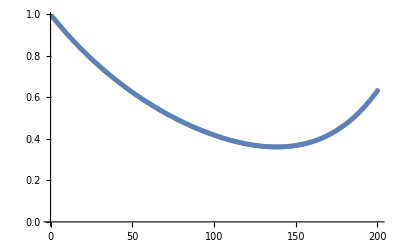

```mathematica
ListPlot[Hereplot*3.5]
```

```mathematica
phiMinTableduration
```

{{{2.54157,3.01275,3.27451,3.90696,0.984419,0.695028,0.939531},{0.918492,3.00513,2.59934,1.63521,0.879898,0.295179,0.234657},{2.2436,2.86151,2.34886,1.53698,0.667144,0.238526,2.02662},{2.82912,2.90405,2.37425,1.54986,0.597768,0.134913,0.675103},{2.24086,2.75968,3.32273,3.87977,3.47087,1.46161,1.12657},{1.82715,2.99789,2.56602,1.61106,0.818332,0.281381,0.373947},{2.02003,1.68279,-0.331701,-0.739043,-0.185281,0.379691,0.928339},{-0.799139,0.35836,1.00262,1.52911,2.06577,2.66248,3.71235},{3.02527,2.99268,2.47861,1.5749,0.699541,0.176335,0.457527},{4.87497,0.21037,0.991468,1.52792,2.0969,2.78513,4.27912},{3.26349,3.06706,2.55201,1.58271,0.758996,0.172404,-0.0240854},{2.36473,3.01952,2.5954,1.6134,0.837076,0.317548,0.476318},{-0.687932,0.375083,0.996452,1.51306,2.03553,2.59974,3.48091},{-1.16732,0.626828,1.30562,1.73754,2.39421,-1.29944,-1.04246},{3.06529,3.02238,2.53264,1.58632,0.754319,0.21706,0.503037},{2.37514,2.98153,2.49605,1.5809,0.726357,0.199472,0.162328},{2.29778,2.75011,2.25501,1.51058,0.508775,0.0959864,0.679172},{1.73175,1.53544,-1.50578,2.255,3.86791,2.03453,1.54331},{2.60664,2.93355,2.39187,1.55606,0.606434,0.112791,0.0285748},{2.78459,2.90097,2.36626,1.54956,0.586122,0.120633,0.394743},{3.83435,0.819862,1.39734,1.81804,2.27162,3.05041,4.37583},{0.303699,3.11455,2.79899,1.68093,1.02025,0.446241,0.743905},{1.19962,2.94294,2.52664,1.62097,0.834367,0.309102,0.730641},{2.81162,2.97476,2.43398,1.56435,0.641887,0.12369,-0.00126416},{-1.13873,0.145652,0.888945,1.38544,1.91751,2.43688,3.21128},{1.42887,1.98493,1.73607,1.37947,-0.02401,-0.229541,2.45274},{1.97217,1.65431,-0.314323,-0.726998,-0.150436,0.394231,0.889367},{2.49768,3.04983,2.62623,1.61167,0.838236,0.30847,0.514653},{1.44378,2.28578,1.94217,1.43718,0.227806,-0.146477,-0.273906},{-0.868475,0.39421,1.04278,1.59231,2.1327,2.81277,4.1337},{2.69685,2.95157,2.42814,1.5639,0.650234,0.147022,0.189703},{2.57434,2.97027,2.473,1.57488,0.701803,0.188728,0.324852},{2.69138,2.89251,2.3398,1.5454,0.539555,0.0807637,0.132631},{3.90454,4.21979,0.751149,1.08657,1.20428,-0.0493353,-0.0386832},{2.67297,3.15893,3.52646,-2.1612,0.683145,0.507258,0.744073},{2.60517,2.89566,2.37586,1.55144,0.608039,0.137706,0.356106},{2.7404,2.95269,2.44488,1.56836,0.675805,0.174031,0.360549},{2.23498,2.74499,3.27936,3.86986,3.45409,1.48423,1.15881},{2.77953,2.89721,2.3303,1.5456,0.528977,0.0677152,0.0023245},{2.62403,2.86128,2.32736,1.53939,0.544371,0.100415,0.336409},{3.20334,3.06844,2.55501,1.58288,0.757073,0.171945,0.0266246},{3.08272,2.98093,2.44233,1.56723,0.653071,0.136247,0.293469},{-0.805696,0.27099,0.916011,1.41577,1.91466,2.41965,3.00058},{2.78577,3.03365,2.58003,1.59733,0.796125,0.260121,0.442162},{2.42702,2.79243,3.47188,3.89989,3.51241,1.42281,1.09228},{-0.709281,0.521008,1.12068,1.69544,2.20557,3.01547,-1.76162},{-0.408537,0.501247,1.07554,1.59451,2.11138,2.70789,3.68812},{1.29609,2.89707,2.45999,1.59484,0.765541,0.254368,0.668663},{2.26718,2.76087,3.3325,3.87946,3.47216,1.46277,1.13257},{2.14545,2.71572,3.19267,3.84624,3.42134,1.53996,1.2354},{2.32363,2.82984,2.32178,1.52761,0.605686,0.181002,1.47915},{-1.12536,0.0810217,0.829018,1.30971,1.79953,2.26087,2.69254},{2.70791,2.8913,2.3262,1.54427,0.522499,0.0639841,-0.000267686},{-0.95228,0.370954,1.02615,1.58095,2.09727,2.86682,-1.52858},{2.30641,2.75031,3.31383,3.86728,3.45909,1.49068,1.18281},{2.16749,2.74549,3.26355,3.87154,3.45301,1.48014,1.1452},{1.79257,2.95507,2.50409,1.59628,0.773423,0.248108,0.32714},{3.00557,3.01921,2.5265,1.58382,0.740262,0.205047,0.498844},{-1.05981,0.393611,1.0609,1.63428,2.16383,2.95752,-1.72614},{1.98962,1.64979,-0.300661,-0.724246,-0.0771447,0.400155,1.12394},{0.52822,0.879551,1.33939,1.8158,2.30116,3.00638,4.16628},{2.17442,2.96278,2.50326,1.58994,0.756562,0.24589,0.43538},{2.64233,2.83408,2.25137,1.53531,0.412965,-0.0024923,-0.177176},{1.97855,1.65477,-0.310445,-0.727411,-0.13276,0.398027,0.900558},{2.54016,3.01992,2.60519,1.61849,0.85154,0.349608,0.757151},{2.58781,2.93599,2.44523,1.56968,0.690598,0.204899,0.685583},{0.00420196,0.683425,1.202,1.7128,2.21587,2.87044,3.97726},{2.98904,2.97352,2.44645,1.56814,0.665366,0.15342,0.337445},{2.04852,2.96312,2.48239,1.58208,0.730677,0.199805,0.0533508},{2.92606,2.98081,2.44239,1.5668,0.658322,0.135359,0.064174},{2.42945,2.79353,3.4828,3.89982,3.51441,1.42328,1.09682},{0.879581,2.92036,2.4924,1.61056,0.800979,0.255657,0.522144},{-1.00959,0.317236,1.00355,1.54296,2.09446,2.74232,4.01884},{2.87837,2.93707,2.39001,1.55643,0.599431,0.111197,0.193613},{2.30603,2.75476,3.32568,3.87066,3.46383,1.48326,1.17252},{3.00433,2.89698,2.33085,1.53181,0.60082,0.160222,1.77572},{2.5719,3.07103,3.36447,3.98695,0.871824,0.620146,0.914469},{2.37474,2.88412,2.39726,1.5567,0.684176,0.234885,1.30301},{4.73511,0.303544,1.05805,1.5985,2.14808,2.87836,4.37983},{0.542301,0.866015,1.31897,1.77803,2.25237,2.84907,3.64188},{2.54628,3.0213,3.28919,3.91435,0.971274,0.686442,0.937236},{-0.346291,0.512689,1.07873,1.59192,2.10485,2.68954,3.62182},{1.98366,1.641,-0.293414,-0.720131,-0.0479874,0.40135,1.22656},{1.9961,1.66939,-0.322993,-0.733774,-0.169786,0.386816,0.880963},{2.60277,2.83745,2.29606,1.51712,0.586476,0.17058,1.86614},{-0.865488,0.443936,1.0756,1.64678,2.16622,2.96004,-1.69764},{3.15209,3.10439,2.65147,1.59385,0.822921,0.236482,0.193593},{2.58148,2.93765,2.39375,1.55661,0.610821,0.111251,-0.0431036},{2.50841,2.97119,3.21514,3.84876,1.07206,0.756331,1.04018},{2.73159,2.86717,2.32295,1.53962,0.531706,0.0847204,0.355081},{2.02363,1.69825,-0.352747,-0.747537,-0.272019,0.36312,0.779995},{3.13967,3.01019,2.47522,1.57295,0.687404,0.14435,0.142584},{2.23584,2.7301,3.24467,3.8562,3.43763,1.51594,1.20866},{1.5254,2.96827,2.52245,1.60417,0.794749,0.245916,0.21805},{2.90954,2.9005,2.33219,1.54665,0.52096,0.0628325,0.154638},{-0.53006,0.435284,1.0294,1.54458,2.062,2.63216,3.52391},{3.40051,3.17703,2.748,1.59728,0.903032,0.285629,0.0145856},{-0.884852,0.268818,0.934049,1.44107,1.96138,2.49328,3.25213},{2.21997,2.9568,2.48925,1.5848,0.740478,0.229637,0.353744},{3.01458,2.86687,2.26527,1.50877,0.532363,0.12291,2.28455}}}